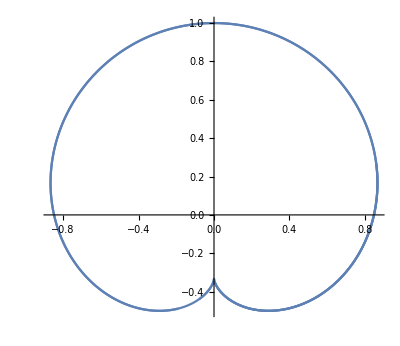

```mathematica
ClearAll["Global`*"]
F[x_,y_,t_]:=Sin[2Pi*4t/2^Floor[Log[4t]]-2Pi*t/2^Floor[Log[t]]]-y(Sin[2Pi*4t/2^Floor[Log[4t]]]-Sin[2Pi*t/2^Floor[Log[t]]])-x(Cos[2Pi*4t/2^Floor[Log[4t]]]-Cos[2Pi*t/2^Floor[Log[t]]]);
Fd[x_,y_,t_]:= 2Pi(
4/2^Floor[Log[4t]]*(Cos[2Pi*t/2^Floor[Log[t]]-2Pi*4t/2^Floor[Log[4t]]]-y*Cos[2Pi*4t/2^Floor[Log[4*t]]]+x*Sin[2Pi*4t/2^Floor[Log[4t]]])
-1/2^Floor[Log[t]]*(Cos[2Pi*t/2^Floor[Log[t]]-2Pi*4t/2^Floor[Log[4t]]]-y*Cos[2Pi*t/2^Floor[Log[t]]]+x*Sin[2Pi*t/2^Floor[Log[t]]])
);
parametricFunc[t_]:={x,y}/.(Solve[F[x,y,t]==0&&Fd[x,y,t]==0,{x,y}]);
ParametricPlot[parametricFunc[t],{t,0,2}]
```